```mathematica
V = 30;
th = 50*π/180;
vt = 100;
g=9.8
ode2 = {x''[t] == (-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2],y''[t] == -g (1 + (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]),x[0] == 0,x'[0]==V*Cos[ 50*π/180],y[0]== 2,y'[0]== V*Sin[ 50*π/180]}
```

9.8

{x''[t]==-0.00098 x'[t] √(x'[t]^2+y'[t]^2),y''[t]==-9.8 (1+(y'[t] √(x'[t]^2+y'[t]^2))/10000),x[0]==0,x'[0]==30 Sin[(2 π)/9],y[0]==2,y'[0]==30 Cos[(2 π)/9]}

```mathematica
{x''[t]==-0.0009800000000000002 x'[t] √(x'[t]^2+y'[t]^2),y''[t]==-9.8 (1+(y'[t] √(x'[t]^2+y'[t]^2))/10000),x[0]==0,x'[0]==30 Sin[(2 π)/9],y[0]==2,y'[0]==30 Cos[(2 π)/9]}
```

{x''[t]==-0.00098 x'[t] √(x'[t]^2+y'[t]^2),y''[t]==-9.8 (1+(y'[t] √(x'[t]^2+y'[t]^2))/10000),x[0]==0,x'[0]==30 Sin[(2 π)/9],y[0]==2,y'[0]==30 Cos[(2 π)/9]}

```mathematica
sol = NDSolve[ode2,{x,y},{t,0.1,200}]
```

{{x→InterpolatingFunction[{{0.1,200.}},<>],y→InterpolatingFunction[{{0.1,200.}},<>]}}

InterpolatingFunction::dmval: Input value {0.00204082} lies outside the range of data in the interpolating function. Extrapolation will be used.

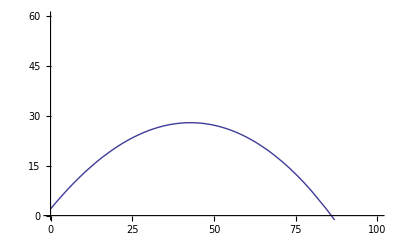

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,100},PlotRange->{{0,100},{0,60}}]
```

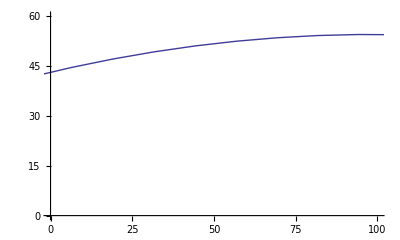

```mathematica
ParametricPlot[{V Cos[th*t],1+V Sin[th*t]-.5g t^2},{t,0,100},PlotRange->{{0,100},{0,60}}]
```

```mathematica
Manipulate[
Module[
{result =NDSolve[{x''[t] == (-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2],y''[t] == -g (1 + (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]),x[0] == 0,x'[0]==V*Cos[ th],y[0]== yo,y'[0]== V*Sin[ th]},{x,y},{t,0,200}]},ParametricPlot[Evaluate[{x[t],y[t]}/.result],{t,0,tf},PlotRange->{{0,150},{0,150}}]],{{V,30,"Velocity(m/s)"},15,100,Appearance->"Labeled"},{{th, 50*π/180,"initial angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{yo, 0,"inintial height (m)"},0.,2.,Appearance->"Labeled"},
{{tf, 20,"time (s)"},0.1,20.,Appearance->"Labeled"},
{{vt,100,"terminal speed (m/s)"},0,200.,Appearance->"Labeled"}]
```

# Cilvil war cannon ball

```mathematica
Manipulate[
m= 6;
G = 9.8;
CC=0.5;
pair=1.29;
A=9.9*10^-3;
vt=135;


Module[
{result =NDSolve[{x''[t] == (-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2],y''[t] == -g (1 + (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]),x[0] == 0,x'[0]==V*Cos[ th],y[0]== yo,y'[0]== V*Sin[ th]},{x,y},{t,0,200}]},ParametricPlot[Evaluate[{x[t],y[t]}/.result],{t,0,tf},PlotRange->{{0,150},{0,150}}]],{{V,30,"Velocity(m/s)"},15,100,Appearance->"Labeled"},{{th, 50*π/180,"initial angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{yo, 0,"inintial height (m)"},0.,2.,Appearance->"Labeled"},
{{tf, 20,"time (s)"},0.1,20.,Appearance->"Labeled"}]
```

# Human cannonball

```mathematica
Manipulate[
vt=60;


Module[
{result =NDSolve[{x''[t] == (-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2],y''[t] == -g (1 + (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]),x[0] == 0,x'[0]==V*Cos[ th],y[0]== yo,y'[0]== V*Sin[ th]},{x,y},{t,0,200}]},ParametricPlot[Evaluate[{x[t],y[t]}/.result],{t,0,tf},PlotRange->{{0,150},{0,150}}]],{{V,30,"Velocity(m/s)"},15,100,Appearance->"Labeled"},{{th, 50*π/180,"initial angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{yo, 0,"inintial height (m)"},0.,2.,Appearance->"Labeled"},
{{tf, 20,"time (s)"},0.1,20.,Appearance->"Labeled"}]
vt
```

135

# Golfball

```mathematica
Manipulate[
vt=44;


Module[
{result =NDSolve[{x''[t] == (-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2],y''[t] == -g (1 + (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]),x[0] == 0,x'[0]==V*Cos[ th],y[0]== yo,y'[0]== V*Sin[ th]},{x,y},{t,0,200}]},ParametricPlot[Evaluate[{x[t],y[t]}/.result],{t,0,tf},PlotRange->{{0,150},{0,150}}]],{{V,30,"Velocity(m/s)"},15,100,Appearance->"Labeled"},{{th, 50*π/180,"initial angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{yo, 0,"inintial height (m)"},0.,2.,Appearance->"Labeled"},
{{tf, 20,"time (s)"},0.1,20.,Appearance->"Labeled"}]
vt
```

60

```mathematica
Manipulate[
vt=43;


Module[
{result =NDSolve[{x''[t] == (-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2],y''[t] == -g (1 + (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]),x[0] == 0,x'[0]==V*Cos[ th],y[0]== yo,y'[0]== V*Sin[ th]},{x,y},{t,0,200}]},ParametricPlot[Evaluate[{x[t],y[t]}/.result],{t,0,tf},PlotRange->{{0,150},{0,150}}]],{{V,30,"Velocity(m/s)"},15,100,Appearance->"Labeled"},{{th, 50*π/180,"initial angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{yo, 0,"inintial height (m)"},0.,2.,Appearance->"Labeled"},
{{tf, 20,"time (s)"},0.1,20.,Appearance->"Labeled"}]
vt
```

44

# Part a table in python here bellow is part b note 5 degrees = .0876 rad 10 degrees =.1753 rad 15 degrees= .2617 rad

```mathematica
Manipulate[
vt=135;
V = 439;

Module[
{result =NDSolve[{x''[t] == (-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2],y''[t] == -g (1 + (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]),x[0] == 0,x'[0]==V*Cos[ th],y[0]== yo,y'[0]== V*Sin[ th]},{x,y},{t,0,2000}]},ParametricPlot[Evaluate[{x[t],y[t]}/.result],{t,0,tf},PlotRange->{{900,8000},{-10,500}}]],{{th, 50*π/180,"initial angle (rad)"},.0876,π/2,Appearance->"Labeled"},
{{yo, 0,"inintial height (m)"},0.,2.,Appearance->"Labeled"},
{{tf, 20,"time (s)"},0.1,20.,Appearance->"Labeled"}]
vt
```

43

# table for part b on python

```mathematica
Manipulate[
vt=135;

Module[
{result =NDSolve[{x''[t] == (-g x'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2],y''[t] == -g (1 + (y'[t]/vt^2) Sqrt[x'[t]^2 + y'[t]^2]),x[0] == 0,x'[0]==V*Cos[ th],y[0]== yo,y'[0]== V*Sin[ th]},{x,y},{t,0,2000}]},ParametricPlot[Evaluate[{x[t],y[t]}/.result],{t,0,tf},PlotRange->{{500,3000},{-10,500}}]],
{{V,30,"Velocity(m/s)"},15,400,Appearance->"Labeled"},
{{th, 50*π/180,"initial angle (rad)"},.0876,.2617,Appearance->"Labeled"},
{{yo, 0,"inintial height (m)"},0.,2.,Appearance->"Labeled"},
{{tf, 20,"time (s)"},0.1,20.,Appearance->"Labeled"}]
```